Towards A Theory for the Speed of Biological Evolution

Willem Nielsen

It took thousands of years of civilized life before the Laws of Physical Motion crystalized. In a way, it makes sense, because when you observe all the different types of motion that occur, it’s not clear that there is any universality. Things move at different speeds, in different directions, with different accelerations, depending on their mass, and the mass of objects around them. But, almost remarkably, there are laws that all these situations follow, first defined in Newton’s Principia. 

In biology, we have defined evolution as a powerful and wide-reaching explanation for the different life forms we observe here on earth. However, the speed at which evolution proceeds in different situations, what you could call “The Laws of Biological Motion” are still up in the air. Many biologists will likely say that this is because they do not exist, or that they are too complex to define with simple statements. But, as we saw in physics, it can take a while for laws to show themselves, so I think this is still a worthwhile question to explore.

To find the rates of  biological evolution in different situations, I will use the model from Stephen Wolfram’s blog post, with some minor modifications to fit our needs. In Wolfram’s model he defines rules for computational programs as genes, and the results of those programs as the organism. He defines the metric of fitness to be the length at which those automata run (excluding infinite). He defines the evolutionary process to be the search for automata of the same or longer length than the current automata. This works well for modeling how life can go from simple to complex, but for our purposes of observing speed, it’s helpful to get even more minimal.

Genes and organisms are the same, but we will define the evolutionary process as starting from initial automata, and finding new automata of the same length as the initial. The speed of evolution is therefore the rate of discovery of new automata.

Starting with this rule:

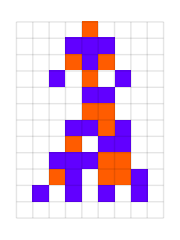

```mathematica
plot[initrule, ImageSize->Small]
```

```mathematica
26^3
```

17576

Just like Wolfram, we define a point mutation as flipping one of the colors in the rule like so:

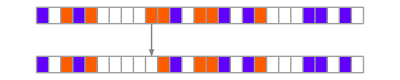

```mathematica
rulesmutationplot[{initrule, getmutation[initrule, 10][[1]]}]
```

We do all possible point mutations starting from the initial rule:

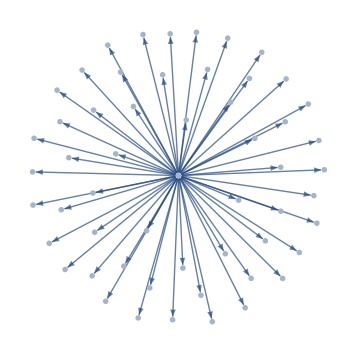

```mathematica
NestGraph[getallmutations, {initrule}, 1, VertexShapeFunction->(Inset[plotrule[#2, ImageSize->100], #1]&)]
```

And here is the resulting automata:

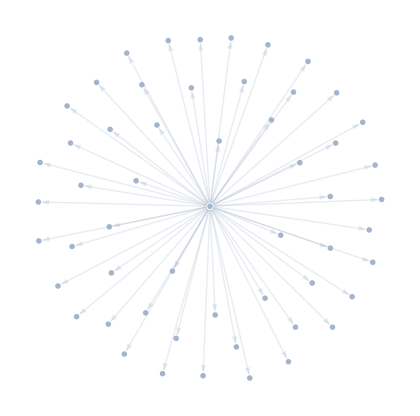

```mathematica
ng = NestGraph[getallmutations, {initrule}, 1, VertexShapeFunction->(Inset[plot[#2, ImageSize->20, "init"->initconditions2], #1]&), EdgeStyle->Opacity[0.1]]
```

We then keep only the ones that run for exactly 11 steps. That is, ones that are the same length as the original:

```mathematica
tohigh = Select[EdgeList[ng], testlifetime[#[[2]]] == 11&];
ng2 = NestGraph[getallmutations, {initrule}, 1, VertexLabels->{x_:>Placed[If[testlifetime[x] == 11, plotfix[x, ImageSize->20, "init"->initconditions2], ""],Center]}, VertexSize->0, EdgeStyle->Opacity[0.1]];
HighlightGraph[ng2, tohigh]
```

-Graphics-

Now we simply recurse,  getting all the mutations for our newly selected automata, and from those selecting the automata of length 11:

```mathematica
newts = getneutral[initrule];
allmutes = getallmutations/@ newts;
edge[rule_, mutes_]:=rule->#&/@ mutes
alledges = MapThread[edge, {newts, allmutes}];
g = Graph[Join[tohigh, Flatten[alledges, 1]]];
bfs = Reap[BreadthFirstScan[g, 
  initrule,{"FrontierEdge"->Sow}]][[2, 1]];
bfsg = Graph[bfs,VertexLabels->{x_:>Placed[If[testlifetime[x] == 11, plotfix[x, ImageSize->10, "init"->initconditions2], ""],Center]}, VertexSize->0, EdgeStyle->Opacity[0.1]];
HighlightGraph[bfsg, tohigh]
```

-Graphics-

And we can continue this process. Going one more step and only showing the selected automata:

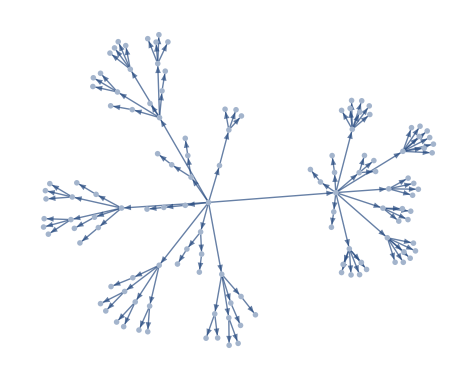

```mathematica
ng = NestGraph[getneutral, {initrule}, 3, VertexShapeFunction->(Inset[plot[#2, ImageSize->20, "init"->initconditions2], #1]&)];
bfs = Reap[BreadthFirstScan[ng, 
  initrule,{"FrontierEdge"->Sow}]][[2, 1]];
bfsg = Graph[bfs,VertexShapeFunction->(Inset[plot[#2, ImageSize->15, "init"->initconditions2], #1]&)]
```

Almost all of these have the exact same “phenotype”. So we can simplify by only showing different phenotypes. Here is that same graph, phenotypically reduced:

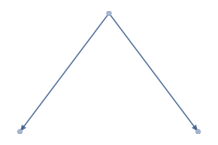

```mathematica
ef = DeleteDuplicatesBy[pgmemo[[2]], Sort];
fg = Graph[ef,VertexShapeFunction->(Inset[plotca[#2, ImageSize->{28, 42}], #1]&) , GraphLayout->"LayeredEmbedding", EdgeShapeFunction->{{ "Arrow", "ArrowSize"->0.05}}, AspectRatio->2/3]
```

Pretty underwhelming, and when I was exploring this space, I didn’t expect to get anything much more interesting than this. But let’s search a bit deeper and see what happens. Here we show going 6 steps deep:

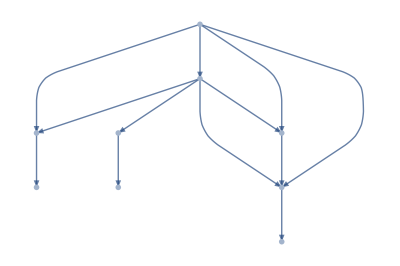

```mathematica
ef = DeleteDuplicatesBy[pgmemo[[5]], Sort];
fg = Graph[ef,VertexShapeFunction->(Inset[plotca[#2, ImageSize->{28, 42}], #1]&) , GraphLayout->"LayeredDigraphEmbedding", EdgeShapeFunction->{{ "Arrow", "ArrowSize"->0.05}}, AspectRatio->2/3]
```

Things are moving a bit faster, not only are we discovering more automata, but they are looking very different from each other and from our initial one. Going 9 steps deep we get:

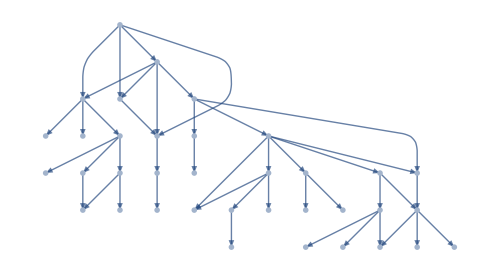

```mathematica
ef = DeleteDuplicatesBy[pgmemo[[8]], Sort];
Graph[ef,VertexShapeFunction->(Inset[plotca[#2, ImageSize->{30, 40}], #1]&) , GraphLayout->"LayeredDigraphEmbedding", EdgeShapeFunction->{{ "Arrow", "ArrowSize"->0.025}}]
```

Again, we’re moving faster, with many new “ideas”. At 11 steps we get:

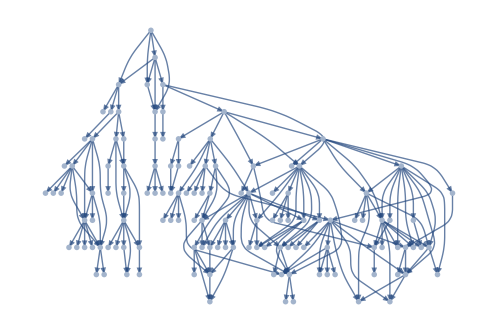

```mathematica
ef = DeleteDuplicatesBy[pgmemo[[10]], Sort];
Graph[ef,VertexShapeFunction->(Inset[plotca[#2, ImageSize->{18, 30}], #1]&) , GraphLayout->"LayeredDigraphEmbedding", EdgeShapeFunction->{{ "Arrow", "ArrowSize"->0.01}}, AspectRatio->2/3]
```

So we’re seeing a large speedup in the discovery process. To give you a sense for the rate of discovery, here we show the discoveries made in each of the first 6 steps:

```mathematica
Column[Row/@clean[[;;6]]]
```

-Graphics--Graphics-
-Graphics-
-Graphics--Graphics-
-Graphics-
-Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics--Graphics-

And here are the discoveries of the last 4 steps:

```mathematica
GraphicsRow[ggs[[7;;]]]
```

-Graphics-

And in a way, this makes sense, because we’re searching a 26-dimensional space, so as we go deeper we’re searching a lot more nodes. Here’s a graph showing the number of nodes searched:

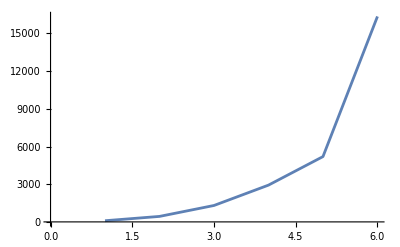

```mathematica
ListLinePlot[Length/@ mgmemo]
```

And here’s the graph of new automaton discovered, or what we defined as the speed of evolution:

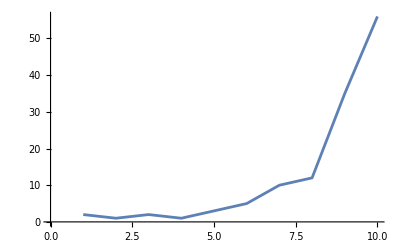

```mathematica
ListLinePlot[Length/@ clean]
```

### Are we expanding into phenotype space?

One question here is, “Are we just getting more ‘species’ or are we actually getting more diversity”.  In other words, are we moving inwards, getting a more and more detailed graph? Or are we actually expanding out into phenotype space? And if you look at the progressive phenotype graphs below, it’s not clear whether we’re actually expanding our graph in phenotype space.

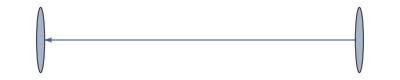
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Graph[#]&/@ pgmemo
```

To answer this we can graph all our automata in feature space, and progressively add the automata at each step. If the automata appear to spread out, then we know they’re actually breaking new ground.

```mathematica
fspmulti
```

-Graphics-

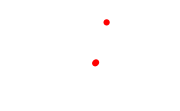
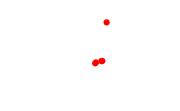
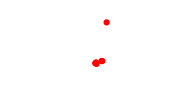
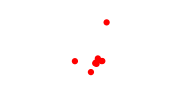
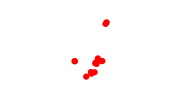
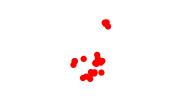
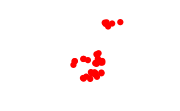
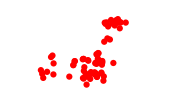
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
acc = Accumulate[Length/@ clean];
ListPlot[coordsmulti[[;;#]],PlotRange->{{-15, 15},{-15, 15}}, ImageSize->Small, PlotStyle->{PointSize[0.025],Red}, Axes->False, PlotHighlighting->None]&/@ acc
```

So it appears that it is expanding into feature space, although not at every step. For instance, the jump between 8 and 9 gives a huge expansion, but between 9 and 10 we mostly move inward.

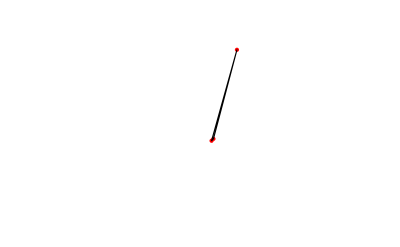
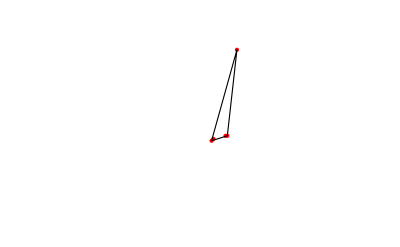
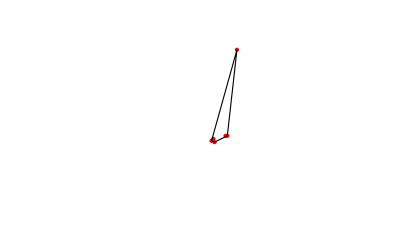
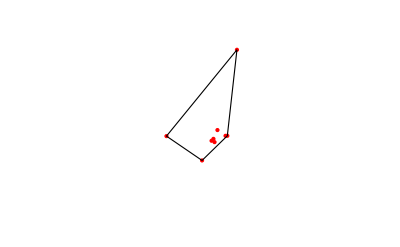
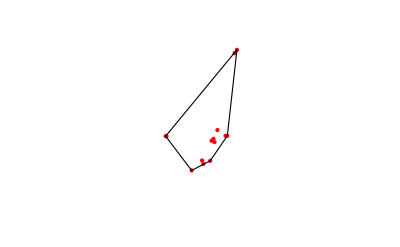
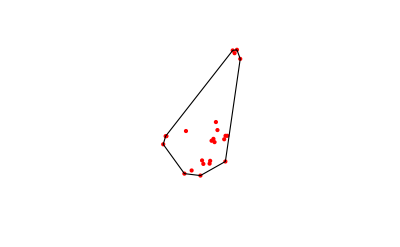
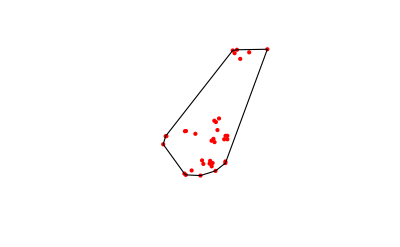
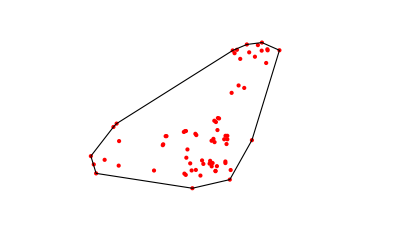

```mathematica
hulls=ConvexHullMesh[coordsmulti[[;;#]]]&/@ acc[[2;;]];
MapThread[Show[ListPlot[coordsmulti[[;;#1]],PlotStyle->{Red,PointSize[Small]}, PlotRange->{{-15, 15},{-15, 15}}, Axes->False],Graphics[{EdgeForm[Black],FaceForm[None],#2}]]&, {acc[[2;;]], hulls}]
```

Here we plot the area of each region.

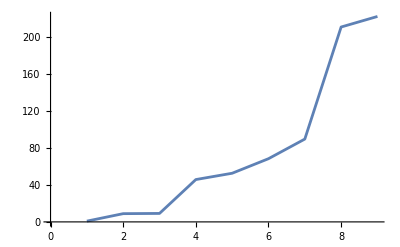

```mathematica
ListLinePlot[RegionMeasure/@ hulls]
```

We’re definitely increasing, and it’s definitely convex up to step 9, but we may be hitting a wall at step 10.

### Overall takeaway

So our first takeaway is the following: When you have a high dimensional genome space, and you search in many different directions (or you could think of this as allowing many different phenotypes to exist at once), then you can get a rapid increase in the rate of evolution, like the one we saw above. This is a simple, but powerful idea. When biological evolution is taught, it is usually taught as if it is one process, as if it has the same properties, whether acting on viruses in Wuhan, rats in Manhattan, lions in the Bronx Zoo, or hamsters in your cousin’s basement. While there is some truth to this, it gives the misguided impression that evolution should have a single speed. In fact, when Darwin conceived of evolution, he assumed it must be a gradual process, because it was seemingly impossible to explain the complex designs otherwise. But Darwin turned out to be wrong about this. In the 70’s, spurred by a reexamination of tiny animal fossils in The Burgess Shale, a new theory emerged. Biologists realized that many of the fossils in the shale were not part of any group known today, as they originally thought. The time period came to be known as “The Cambrian Explosion”. The theory, stating that rapid evolution occurs in short time windows, followed by long stretches of very little change, is called “Punctuated Equilibrium”. And with our example above, we saw how our model agrees with that theory.

So evolution clearly doesn’t have a single speed. But is there still some general law governing it’s motion? Well in the above example we gotten an important hint, . Namely, that the dimensionality of genome space increases the rate of evolution. But can we say something precise about how exactly dimensionality and any other important factors affect the rate of evolution? To do this, it’s helpful to further simplify the model.

### Zooming in on genome space

We’ll now ignore the organism and just focus on the genes. Here we show a very small genome space of 5-bits:

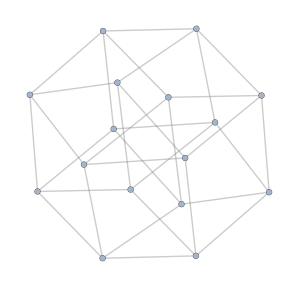

```mathematica
ug = UndirectedGraph[Catenate[Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@Tuples[{1,0},4]],EdgeStyle->Opacity[.4,Gray]];
ug2 = Graph[ug, VertexLabels->{x_:>Placed[ArrayPlot[{Append[x,0]},
Mesh->True,ImageSize->40],Center]}]
```

Now instead of looking for automata of a constant length, we will just randomly define a set of genes to be “fit”. Here we randomly choose 10 genes to be fit:

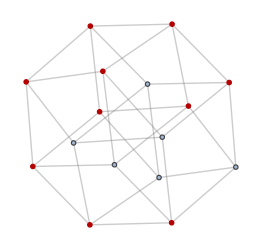

```mathematica
HighlightGraph[ug, rand = RandomSample[VertexList@ug, 10]]
```

So how can evolution move through the “fitness space”? Here’s the subgraph containing only the fit genotypes:

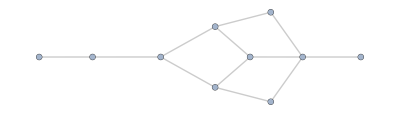

```mathematica
Subgraph[ug2, rand]
```

Things start to get interesting when you increase the size of genome. Here’s a 7-bit genome space:

```mathematica
ug6 = Graph[ugs[[6]], VertexLabels->{x_:>Placed[ArrayPlot[{Append[x,0]},
Mesh->True,ImageSize->40],Center]}]
```

-Graphics-

Taking a random fitness sample we get:

```mathematica
HighlightGraph[ugs[[6]], rand = RandomSample[VertexList@ugs[[6]], 30], VertexSize->0.2]
```

-Graphics-

And here is the fitness space:

```mathematica
Subgraph[ugs[[6]], rand, VertexLabels->{x_:>Placed[ArrayPlot[{Append[x,0]},
Mesh->True,ImageSize->40],Center]}]
```

-Graphics-

Now we’re starting to get to a level of dimensionality that could produce an explosion of new ideas like we saw above. Let’s keep increasing the size of the genome space, here’s a 10-bit genome with a random fitness set of size 250:

```mathematica
ug9 = UndirectedGraph[Catenate[Table[#->MapAt[1-#&,#,i],{i,Length[#]}]&/@Tuples[{1,0},9]],EdgeStyle->Opacity[.4,Gray], VertexSize->0];
HighlightGraph[ug9, rand = RandomSample[VertexList@ug9, 250], VertexSize->0.6]
```

-Graphics-

The fitness space now looks like:

```mathematica
sg = Subgraph[ugs[[9]], rand]
```

-Graphics-

Shown in a different way:

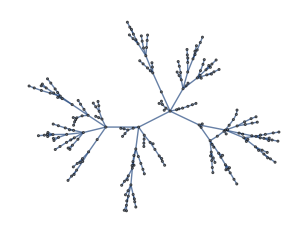

```mathematica
bfs = Reap[BreadthFirstScan[sg, 
  RandomChoice[rand],{"FrontierEdge"->Sow}]][[2, 1]];
bfsg = Graph[bfs]
```

With this graph you can clearly see the outward explosions in diversity that we saw in our example above with the 2-color automata. So we’re seeing that even in a 10-bit genome, if you have multiple organisms and search in multiple directions at once, then explosions can happen. 

One thing I didn’t mention, is how large I’m making the fitness set. And indeed, even with a 10-bit genome, if the fitness set is small, evolution won’t be able to expand quickly. Here we show what happens if our fitness set is only 100 out of 512 genes:

```mathematica
rand = RandomSample[VertexList@ug9, 100];
HighlightGraph[ug9, rand, VertexSize->0.6]
```

-Graphics-

And here’s our fitness space:

```mathematica
sg = Subgraph[ug9, rand]
```

-Graphics-

Here we don’t see nearly as much branching as before, so the speed of evolution will be quite slow. So, we’ve seen two critical factors in the rate of evolution. First, you need to have a genome that is high dimensional. Second, you need enough solutions. But just how high-dimensional? And just how many solutions?

We can look at what happens in the 8-bit case as we add more solutions to get a sense for this:

```mathematica
sgslist[[7, ;;-2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

We defined the speed of evolution to be how fast new automata are discovered. We can do a sample run in each of these fitness spaces, and see the precise rate at which genes

We can see that increasing the number of solutions rapidly increases the connectivity. What if we hold the proportion of solutions constant and increase the dimensionality? Here we show the progression if we keep the solutions to 30% and add dimensions. Again a rapid increase in connectivity:

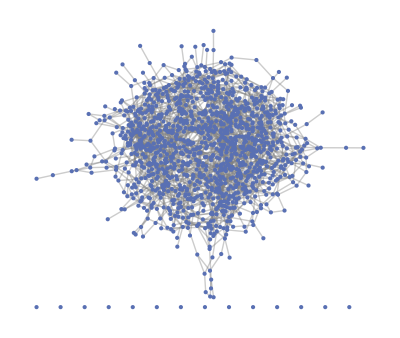
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sgslist[[4;;, 3]]
```

TO BE CONTINUED

### Looking at the speed of single organism evolution

So in his article Wolfram mainly focuses on the programs go from short to long and therefore, from simple to complex. In an attempt to model bacterial resistance, I examined another dimension, that of diversity. One approach is to start with a rule and then explicitly look for “new ideas”. That is, look for automata with the pattern that is most different from any of its predecessors, judged by difference in corresponding boxes.

So we start with this rule here.

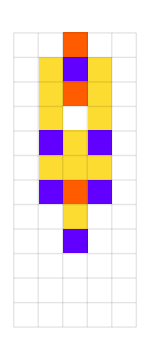

```mathematica
plotfit[#, ImageSize->150]&@trirule
```

Then we generate a bunch of random mutations and select only ones that are about the same length. Of those, we select the one that is most different from the previous automata. In this case, this was the most different. There is a few yellow boxes on the bottom left that are added.

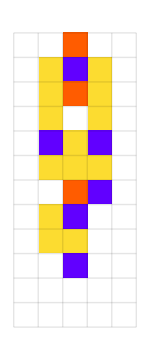

```mathematica
plotfit[ getmostdiff[{trirule}][[-1]], ImageSize->150]
```

We do this recursively and basically ask the question, how different can we get? And somewhat remarkably, this simple procedure is able to continuously find new automata of similar length.

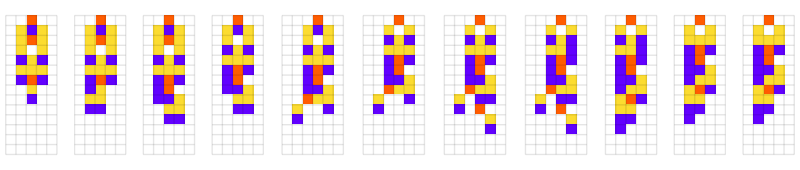

```mathematica
GraphicsRow[plotfit/@diffsmemo[[3]], ImageSize->{800, Automatic}]
```

The way in which this happens varies greatly. In this cases we basically had one radical idea.

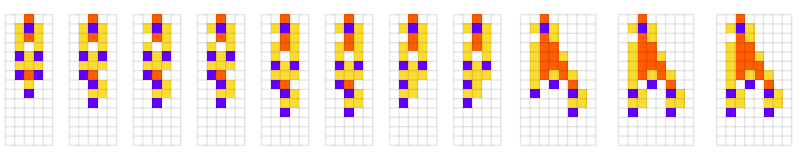

```mathematica
GraphicsRow[plotfit/@diffsmemo[[6]], ImageSize->{800, Automatic}]
```

In this case we get stuck.

```mathematica
GraphicsRow[plotfit[#, ImageSize->60]&/@DeleteCases[diffsmemo[[5]], {}]]
```

-Graphics-

In this case, we have an explosion of new ideas.

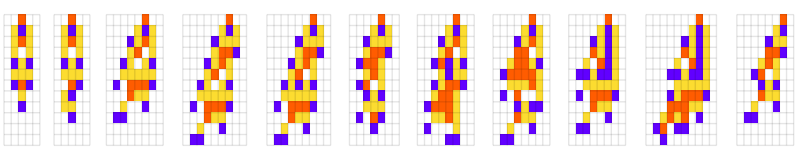

```mathematica
GraphicsRow[plotfit[#]&/@diffsmemo[[10]], ImageSize->{800, Automatic}]
```

And we can see that each time we go in a different direction. This shows us that the space of automata is very rich. So how far can this process go? Here is a run after 30 steps:

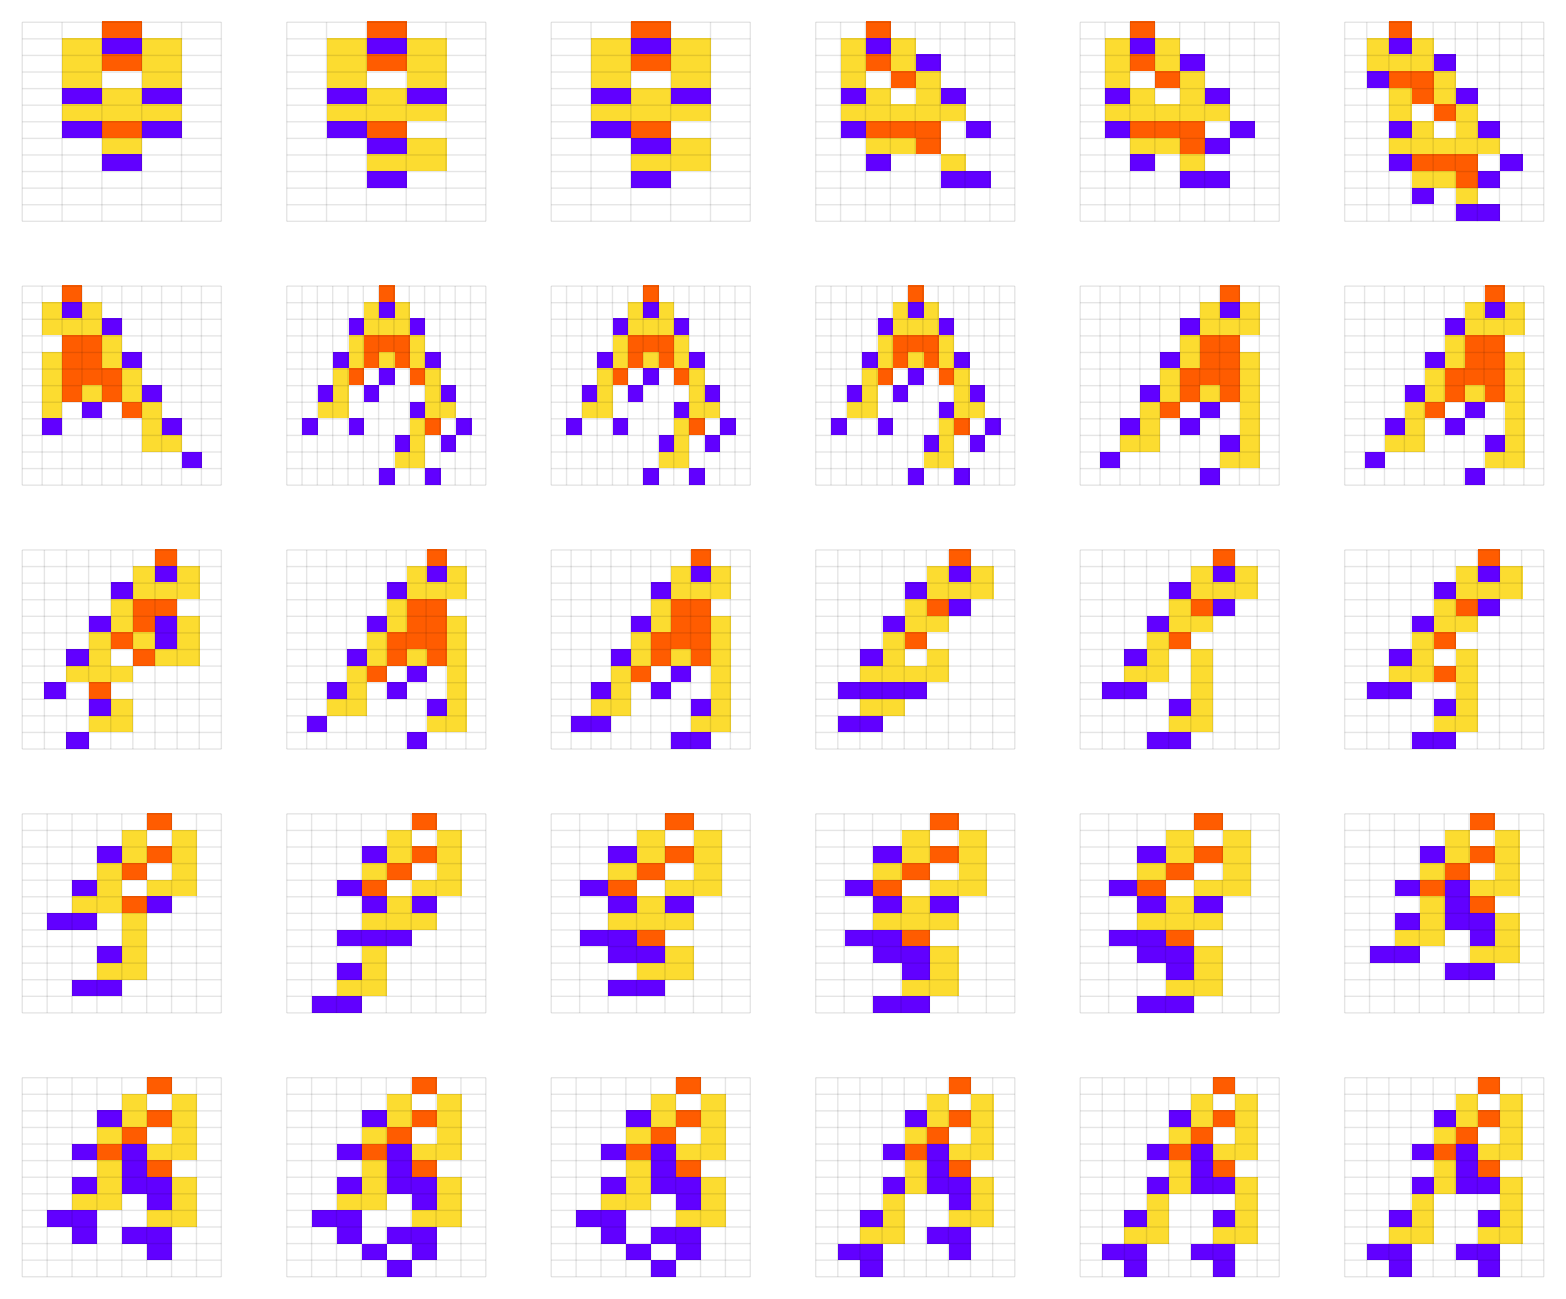

```mathematica
GraphicsGrid[Partition[plotfit[#]&/@diffsmemo[[13]], 6]]
```

Notice how there are new ideas continuously discovered

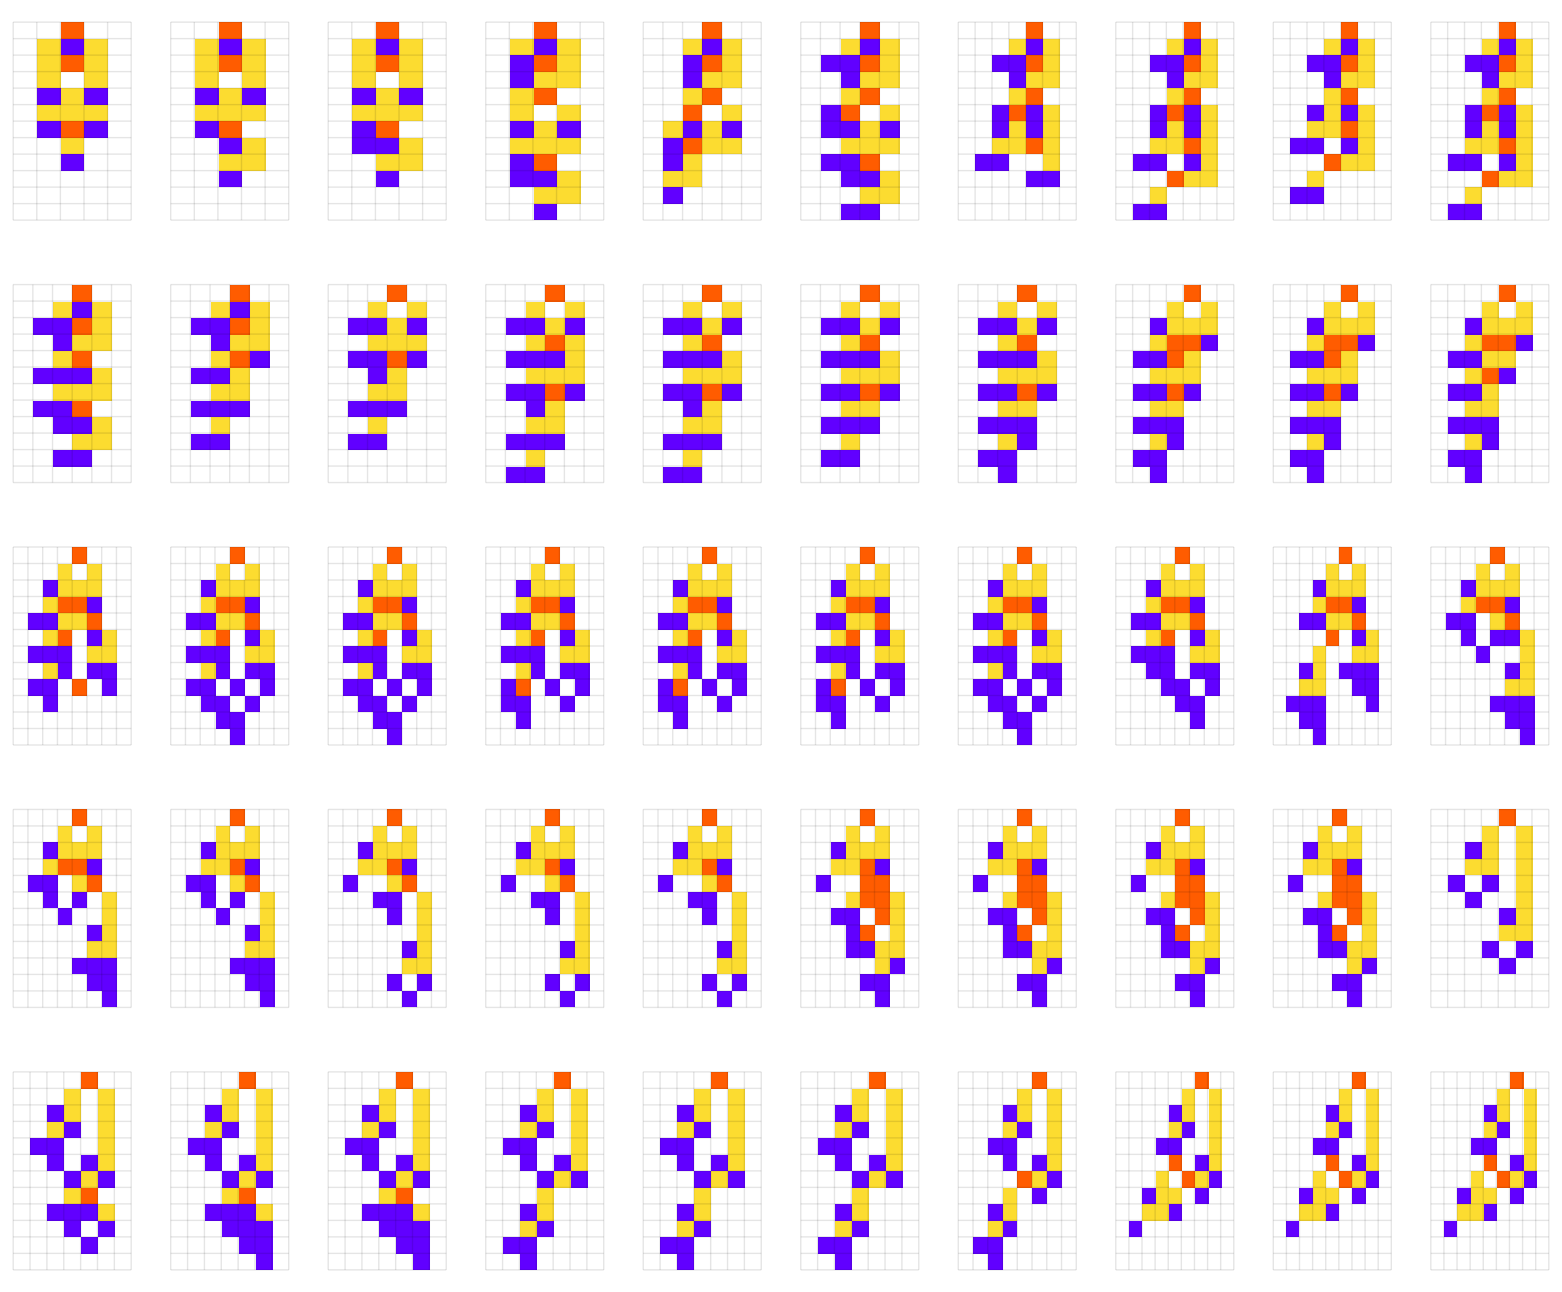

```mathematica
GraphicsGrid[Partition[plotfit/@diffsmemo[[14]], 10]]
```

We can see that process continues to be able to find new solutions. To quantify how the automata change over time, we can look at the number of boxes that are different from the initial automata.

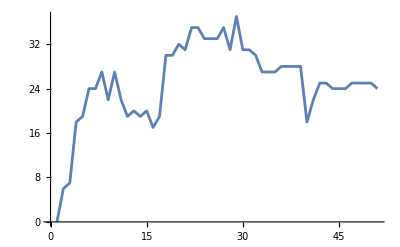

```mathematica
ListLinePlot[getdiffrule[trirule, #]& /@ diffsmemo[[-1]]]
```

One take away here, is the “pace of innovation” seems to jump around a lot. Also, there is a rapid increase at the start followed by a plateauing effect. This is because the automata can only become so different from the initial. But, if we instead use a feature space plot we can get a better sense of  the rate of innovation. Here is that same run with the line darkening over time.

```mathematica
plots = plotfit[#, ImageSize->30]&/@ diffsmemo[[14]];
callouts = MapThread[Callout[#1,Style[#2], Automatic,LeaderSize->15,LabelVisibility->All,Background->None]&, {coords14,plots }];
ListLinePlot[callouts, Mesh->All,MeshStyle->PointSize[0.01],PlotStyle->Directive[Thick,LightGray], PerformanceGoal->"Quality", ColorFunction->Function[{x,y},Blend[{Black, LightGray},x]], Frame->False, Axes->False]
```

-Graphics-

And if we look at the speed of innovation in feature space over time we don’t see the slowdown from before. Here we just take the distances of each step in the plot above.

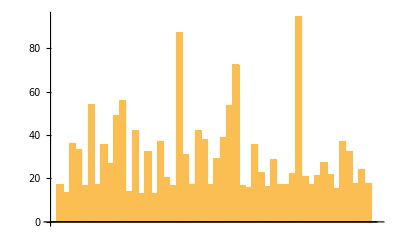

```mathematica
coordpairs = Partition[coords14, 2, 1];
dists = EuclideanDistance@@@coordpairs;
BarChart[dists]
```

And the thing to observe here is while there are large fluctuations, the overall rate of innovation stays pretty much constant, which we will see later is not always the case. So we’ve been looking at k = 4, r = 1 automata, does this work with k = 3?

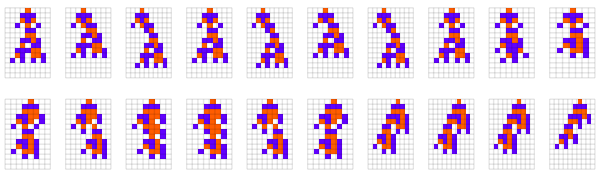

```mathematica
GraphicsGrid[Partition[plotfit/@diffsmemo[[47]], 10], ImageSize->{600, Automatic}]
```

So we can see that it still works, let’s go further with a run of 50 steps.

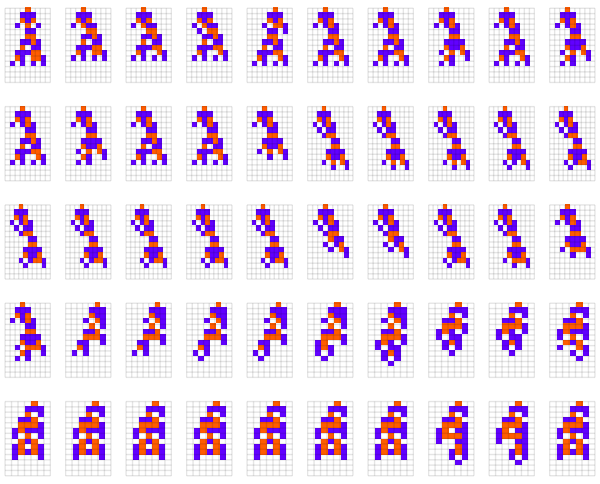

```mathematica
GraphicsGrid[Partition[plotfit/@diffsmemo[[48]], 10], ImageSize->{600, Automatic}]
```

If you look carefully you can see that the 2-color automata tend to get stuck on one idea for longer. This is because there is simply less solutions. Interestingly, when it does make a jump though, the jump is usually huge. This can be seen in the graph of the differences of each automata with the initial automata.

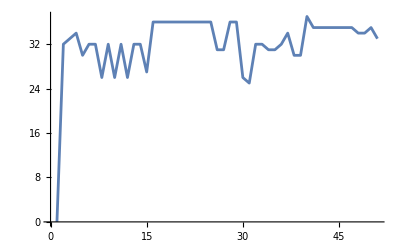

```mathematica
ListLinePlot[getdiffrule[initrule, #]& /@ diffsmemo[[48]]]
```

Notice  how  it  has  a  big  jump  to  30, and  then  has a stretch where it is alternating between two of the same idea:

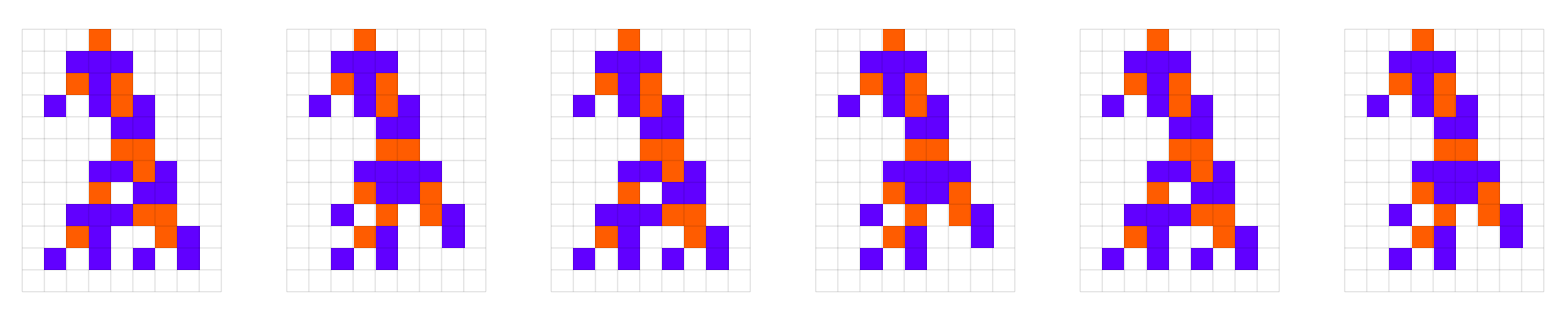

```mathematica
GraphicsRow[plotfit[#]&/@ diffsmemo[[48, 7;;12]]]
```

We never saw something like this with the three color. Now, it’s an interesting question: “How  does evolution vary with each generation?”. Does biological evolution prefer many small changes or a few large ones? I think this an interesting question to pursue; Empirically, it seems that it prefers very small changes and non-random ones. Like the shape of human bodies for example. There is clearly some purposeful distribution of height, weight and dimensions, but you very rarely see someone randomly grow a third leg. Evolution is conservative in this way. I think there is something very deep here related to risk-taking principles that all surviving systems must follow, and I’m going to explore that extensively in a different article.

But okay, let’s look at the feature space plot of the 2-color automata to get a better sense of what’s going on.

```mathematica
plotsk3=(plotfit[#1,ImageSize->22]&)/@diffsmemo⟦48⟧;
callouts = MapThread[Callout[#1,Style[#2], Automatic,LeaderSize->15,LabelVisibility->All,Background->None]&, {coords48, plotsk3 }];
ListLinePlot[callouts, Mesh->All,MeshStyle->PointSize[0.01],PlotStyle->Directive[Thick,LightGray], PerformanceGoal->"Quality", ColorFunction->Function[{x,y},Blend[{LightGray, Black},x]], Frame->False, Axes->False]
```

-Graphics-

Again, we can see that change is less continuous, with a bunch of bouncing around in one place followed by a large jump into a new area. Looking at the “derivative of diversity” below we see a similar theme, with much larger jumps than before:

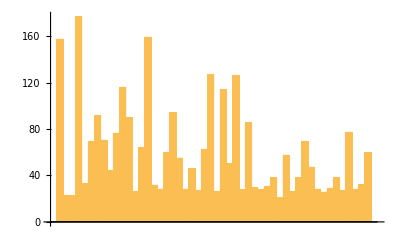

```mathematica
coordpairs = Partition[coords48, 2, 1];
dists = EuclideanDistance@@@coordpairs;
BarChart[dists]
```

We can also note that while the rate fluctuates greatly between individual steps, the overall rate seems to be staying convex, something we’ll see does not hold when we add multiple organisms.

## Functions and Parameters

```mathematica
testlifetime = {{"[◼]", "TestLifetime"}}; randomrulemutation = {{"[◼]", "RandomRuleMutation"}};
rulesmutationplot = {{"[◼]", "RulesMutationPlot"}}; customstyledata = {{"[◼]", "CustomStyleData"}};
```

```mathematica
k = 3; r = 1; initrule = {5586032021307, 3, 1}; trirule = {109636419052937157723438118980837975564,4,1};
longrule = {5600111605818,3,1};
initconditions = {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0};
nsteps = 11; initlifetime = testlifetime[initrule];
```

```mathematica
getca[rule_] := CellularAutomaton[rule, initconditions, nsteps]
```

```mathematica
plot[{ruleidx_, k_, r_}, OptionsPattern[{ColorRules->customstyledata["Colors"], ArrayPlot}]] :=  Module[{ca},
  ca = getca[{ruleidx, k, r}];
  ArrayPlot[ca,  ColorRules->OptionValue[ColorRules],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]]

Options[plotfit] = {"init"->initconditions, "padding"->1, "nsteps"->nsteps};
plotfit[{ruleidx_, k_, r_}, OptionsPattern[{ColorRules->customstyledata["Colors"], plot, ArrayPlot}]] :=  Module[{ca},
  ca = ArrayPad[#, OptionValue["padding"]]& /@ getca[{ruleidx, k, r}, OptionValue["init"], OptionValue["nsteps"]];
  ArrayPlot[ca,  ColorRules->OptionValue[ColorRules],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> OptionValue[ImageSize]
   ]]

plot[ruleidx_Integer] := Module[{ca},
  ca = getca[{ruleidx, k, r}];
  ArrayPlot[ca, ColorRules -> customstyledata["Colors"],
   Mesh -> True, MeshStyle -> Opacity[.1], ImageSize -> {165, Automatic}
   ]]
```

```mathematica
getmostdiff[rules_]:= Module[{auto, mutes, selected, autos, diffs},
 auto = getca[rules[[-1]]];
 mutes = Table[randomrulemutation[rules[[-1]]], 100];
 selected = Select[mutes,withinrange[#, 10, 12]&];
 If[selected == {}, Append[rules, rules[[-1]]],
 Append[rules, TakeLargestBy[selected, getdiffs[rules, #]&, 1][[1]]]]
]
```

```mathematica
ClearAll@phenoedges
```

```mathematica
getcaedge[start_->dest_]:= getca[start]->getca[dest]

phenoedges[graph_]:=Module[{},
es = EdgeList@graph;
caedges = getcaedge/@ EdgeList[graph];
DeleteCases[DeleteDuplicates[caedges],x_->x_]
]
```

## Saving and loading

```mathematica
reglist = Table[
vs = VertexList@Graph[pgmemo[[i]]];
plotca[#, ImageSize->20]&/@vs,{i, 1, 10}];
clean = Module[{f},f[x_]:=(f[x]=Sequence[];x);Map[f,reglist,{2}]];
```

```mathematica
Export["Projects/Wolfram/CAEvolution/diffsmemo/diffsmemo.csv", diffsmemo]
```

Projects/Wolfram/CAEvolution/diffsmemo/diffsmemo.csv

```mathematica
Export["Projects/Wolfram/CAEvolution/diffsmemo/coordsk3.csv", coordsk3]
```

Projects/Wolfram/CAEvolution/diffsmemo/coordsk3.csv

```mathematica
Export["Projects/Wolfram/CAEvolution/graphmemo.csv", graphmemo]
```

Projects/Wolfram/CAEvolution/graphmemo.csv

```mathematica
Export["Projects/Wolfram/CAEvolution/pgmemo.csv", pgmemo]
```

Projects/Wolfram/CAEvolution/pgmemo.csv

```mathematica
Export["Projects/Wolfram/CAEvolution/mgmemo.csv", mgmemo]
```

Projects/Wolfram/CAEvolution/mgmemo.csv

```mathematica
diffsmemocsv = Import["Projects/Wolfram/CAEvolution/diffsmemo/diffsmemo.csv"];
```

```mathematica
diffsmemo = Map[ToExpression, diffsmemocsv, {2}];
```

```mathematica
graphmemocsv = Import["Projects/Wolfram/CAEvolution/graphmemo.csv"];
```

```mathematica
Length/@ graphmemocsv
```

{437,7,2927,21,16352,282,93,3,437,7,1307,15,2927,21,5198,30}

```mathematica
graphmemo = Map[ToExpression, graphmemocsv, {2}];
```

```mathematica
MapIndexed[Export["Projects/Wolfram/CAEvolution/searchgrid/"<>ToString[#2]<>".jpeg", #1]&, gridlist];
```

```mathematica
pgmemocsv = Import["/Users/erichegonzales/Projects/Wolfram/CAEvolution/pgmemo.csv"];
```

```mathematica
pgmemo =  Map[ToExpression, pgmemocsv, {2}];
```

```mathematica
pgmemo[[1, 1]] // Head
```

DirectedEdge

```mathematica
coords48 = Import["Projects/Wolfram/CAEvolution/diffsmemo/coords48.csv"];
```

```mathematica
coords14 = Import["Projects/Wolfram/CAEvolution/diffsmemo/coords14.csv"];
```

```mathematica
Export["Projects/Wolfram/CAEvolution/diffsmemo/coordsmulti.csv", coordsmulti]
```

Projects/Wolfram/CAEvolution/diffsmemo/coordsmulti.csv